## Code Archive

```mathematica
(* 
harmonicAnalysis[a_,b_,c_,d_]:=Block[{p=a,q=b,r=c,s=d,coeff,θ,rotationMat,starMat,ψ,L,W,ϕ},
θ = 0.5ArcTan[(p^2  +r^2 -q^2-s^2),2(p q + r s)];
coeff = {p,q,r,s};
rotationMat = {{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
starMat=Partition[coeff,2,2].rotationMat;
ψ=ArcTan[starMat[[1,1]],starMat[[2,1]]]*(180 /Pi);
ϕ=ArcTan[starMat[[1,2]],starMat[[2,2]]]*(180 /Pi);
L = Norm[{starMat[[1,1]],starMat[[2,1]]}];
W= Norm[{starMat[[1,2]],starMat[[2,2]]}];
{L,W,ψ,ϕ}];
*)
```

```mathematica
(* 
ClearAll@EllipticalFourier;
Options[EllipticalFourier] = {normalize-> True,sizeInvariance-> True,order-> 10,ptsToplot-> 300,locus->{0.,0.},areathreshold-> 2};
EllipticalFourier[mask_,OptionsPattern[]]:=Module[{dXY,dt,t,T,ϕ,contourpositions, contour,contourtour,contourregion,xi,A0,δ,C0,dCval,coeffL,normalizeEFD,ellipticalCoefficients,plotEFD},
contourpositions = PixelValuePositions[MorphologicalPerimeter[mask],1];
contourtour=Last@FindShortestTour[contourpositions];
contour = Part[contourpositions,contourtour];
contourregion=BoundaryMeshRegion[contourpositions,Line@contourtour];
dXY = Differences[contour];
dt=(x↦N@Sqrt[x])[Total/@(dXY^2)];
t = Prepend[Accumulate[dt],0];
T= Last@t;
ϕ = 2 π t/T;

normalizeEFD[coeff_]:= With[
{θ=0.5 ArcTan[(coeff[[1,1]]^2 -coeff[[1,2]]^2 + coeff[[1,3]]^2 -coeff[[1,4]]^2),
2 (coeff[[1,1]] coeff[[1,2]] +coeff[[1,3]] coeff[[1,4]])]},
Block[{coeffList = coeff,ψ,ψr,a,c,θr},
θr[i_Integer]:={{Cos[i θ],-Sin[i θ]},{Sin[i θ],Cos[i θ]}};
coeffList=Partition[#,2,2]&/@coeffList;
coeffList=MapIndexed[(#1.θr[First@#2])&,coeffList];
a=First@Flatten@First@coeffList;
c=(Flatten@First@coeffList)[[3]];
ψ = ArcTan[a,c];
ψr= {{Cos[ψ],Sin[ψ]},{-Sin[ψ],Cos[ψ]}};
coeffList=MapIndexed[Flatten[ψr.#]&,coeffList];
If[OptionValue[sizeInvariance],a= First@First@coeffList;coeffList/=a,coeffList]]
];

ellipticalCoefficients[order_]:= Module[{coeffs,func},
func[list:{{__}..},n_Integer]:=Block[{listtemp =list, const = T/(2 (n^2)( π^2)),phiN= ϕ *n,
dCosPhiN, dSinPhiN,an,bn,cn,dn},
dCosPhiN = Cos[Rest@phiN]-Cos[Most@phiN];
dSinPhiN = Sin[Rest@phiN]-Sin[Most@phiN];
an = const*Total@(dXY[[All,1]]/dt *dCosPhiN);
bn = const*Total@(dXY[[All,1]]/dt*dSinPhiN);
cn = const*Total@(dXY[[All,2]]/dt*dCosPhiN);
dn = const*Total@(dXY[[All,2]]/dt*dSinPhiN);
listtemp[[n]]= {an,bn,cn,dn};
listtemp
];
coeffs = ConstantArray[0,{order,4}];
coeffL= If[OptionValue@normalize,normalizeEFD[#],#]&@Fold[func,coeffs,Range@order]
];

dcCoefficients:=(
xi =  Accumulate[Part[dXY,All,1]]- (dXY[[All,1]]/dt)*Rest@t;
A0= (1/T)*Total@(dXY[[All,1]]/(2 dt) * Differences[t^2] +  xi*dt);
δ = Accumulate[Part[dXY,All,2]]- (dXY[[All,2]]/dt)*Rest@t;
C0= (1/T)*Total@(dXY[[All,2]]/(2 dt) * Differences[t^2] +  δ*dt);
{First@First@contour + A0,Last@First@contour+C0}
);

plotEFD[coeff_]:= Last@Reap@Block[{n = Length@coeff,nhalf,nrow=2,ti,xt,yt,func,θ,
i=OptionValue[ptsToplot],j,regionpts,shortesttour,regiondiff,regiondiffmetric},
nhalf = Ceiling[n/2];
ti = Array[#&,i,{0.,1}];
xt = ConstantArray[OptionValue[locus][[1]],i];
yt = ConstantArray[OptionValue[locus][[2]],i];
regiondiffmetric =100;
j=1;
While[regiondiffmetric>OptionValue[areathreshold],
xt+= coeff[[j,1]] Cos[2 (j) π ti] + coeff[[j,2]] Sin[2 (j) π ti];
yt += coeff[[j,3]]Cos[2(j) π ti] + coeff[[j,4]] Sin[2 (j)π ti];

regionpts=Most@Thread@{xt,yt};
shortesttour = Line@Last@FindShortestTour@regionpts;
regiondiff=BoundaryMeshRegion[regionpts,shortesttour]~RegionDifference~contourregion;
regiondiffmetric = Area[regiondiff]/Area[contourregion] * 100;
Sow@{harmonicAnalysis[Sequence@@coeff[[j]]],Graphics[{{Thick,XYZColor[0,0,1,0.6],Line@Thread[{xt,yt}]},{Thick,Dashed,XYZColor[1,0,0,0.6],Line@contour},Inset[Style[#,{Black,FontSize->12}]&@Text["harmonic: " <> ToString@j]]}]};
j++
] ;
];
ellipticalCoefficients[OptionValue[order]];
plotEFD[coeffL]
];
*)
```

## Initialize

```mathematica
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\96 hours\\EFD.m";
```

```mathematica
?harmonicAnalysis
```

harmonicAnalysis[p_,q_,r_,s_] takes in four Elliptical Fourier Coefficients and outputs the Length, Width and Orientation of the Ellipse

```mathematica
?EllipticalFourier
```

EllipticalFourier[img_Image,opts] takes in a binarized mask representing the object's shape and outputs an array of Fourier Elliptical Coefficients
that describe the shape. A 2 % difference approximation is used by default. Use locus -> "dcCoefficients"

## Chiron positive aggregates

```mathematica
(* 
import all the aggregate masks;
compute max number of harmonics needed to describe the shape to a 98 % accuracy;
draw a PDF of the number of harmonics needed @ 96 hrs 
*)
```

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@96 hours\\chi pos\\";
```

```mathematica
masks=Import/@Flatten@StringCases[Import[dir],p:HoldPattern[___~~"Mask"~~___~~".tif"]:>  dir<>p];
Length@masks
```

37

```mathematica
(* 
resultschipos=(Clear@dcCoefficients;
EllipticalFourier[#,normalize-> False,order->10,ptsToplot-> 200,locus-> dcCoefficients])&/@masks; (* to be used with archived version of code *) 
*)
```

```mathematica
resultschipos=EllipticalFourier[#,normalize-> False,order->10,ptsToplot-> 200,locus-> "dcCoefficients"]&/@masks;
```

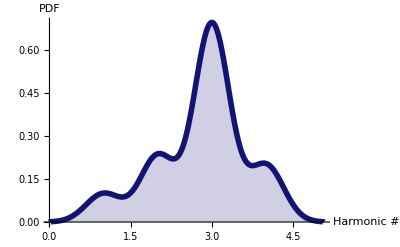

```mathematica
chipos=SmoothHistogram[Length@*First/@resultschipos,PlotStyle->{RGBColor[0.07924700513978256, 0.07394564469935314, 0.4499539624003866],Thickness[0.01]},
Filling->Axis,AxesLabel->(Style[#,{GrayLevel[0.25],13}]&/@{"Harmonic #","PDF"}),
LabelStyle->Directive[Bold,Black,FontSize-> 13],PlotLegends->"RGBColor[0.07924700513978256, 0.07394564469935314, 0.4499539624003866] chi-pos"]
```

## Chiron negative aggregates

```mathematica
(* 
import all the aggregate masks;
compute max number of harmonics needed to describe the shape to a 98 % accuracy;
draw a PDF of the number of harmonics needed @ 96 hrs 
*)
```

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@96 hours\\chi neg\\";
```

```mathematica
masks=Import/@Flatten@StringCases[Import[dir],p:HoldPattern[___~~"Mask"~~___~~".tif"]:>  dir<>p];
Length@masks
```

20

```mathematica
(*
resultschineg=(Clear@dcCoefficients;
EllipticalFourier[#,normalize-> False,order->10,ptsToplot-> 200,locus-> dcCoefficients])&/@masks; (* to be used with archived version of code *)
*)
```

```mathematica
resultschineg=EllipticalFourier[#,normalize-> False,order->10,ptsToplot-> 200,locus-> "dcCoefficients"]&/@masks;
```

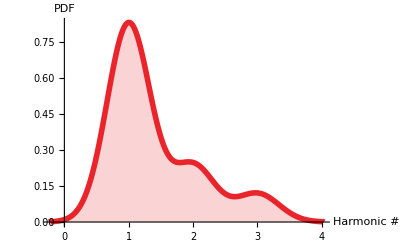

```mathematica
chineg=SmoothHistogram[Length@*First/@resultschineg,PlotStyle->{RGBColor[0.9184512028405248, 0.14170905749799229, 0.16848456616569144],Thickness[0.01]},
Filling->Axis,AxesLabel->(Style[#,{GrayLevel[0.25],13}]&/@{"Harmonic #","PDF"}),
LabelStyle->Directive[Bold,Black,FontSize-> 13],PlotLegends->"RGBColor[0.9184512028405248, 0.14170905749799229, 0.16848456616569144] chi-neg"]
```

## PDFs overlay

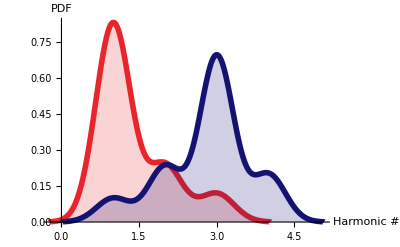

```mathematica
Show[chineg,chipos,PlotRange-> All]
```

```mathematica
Rasterize[Show[chineg,chipos,PlotRange-> All],"Image",ImageResolution->550]
```

-Graphics-